```mathematica
Quit[];
```

```mathematica
Options[singAnal] = {criticalPoint->0, thresholdForApproximation->10^-3, plotThreshold->"NaN",degreeOfApproximation->5,direction->"Both"};
singAnal[f_,OptionsPattern[]] := Block[
{x,
x0=OptionValue[criticalPoint],
thr = OptionValue[thresholdForApproximation],
pltnan = OptionValue[plotThreshold],
n = OptionValue[degreeOfApproximation],
dir = OptionValue[direction],
lim, ser, nser,plt,ass,left,right,
maxrec = 5},
Print["Function:", Style[" f[x] = ",FontSize->Large],Style[f[x],FontSize->Large]];
(*Print["Options:"];
Print["  criticalPoint → ", x0, ","];
Print["  thresholdForApproximation → ", ScientificForm[N[thr,3]], ","];
Print["  degreeOfApproximation → ", n, ","];*)
ass[x_] = Switch[dir,"Left",{x<x0},"Right",{x>x0},"Both",{},_,{}];
Print[ass[x]];
lim = Limit[f[x],x->x0,Assumptions->ass[x]];
Print["Limit: ",Subscript[Subscript["lim","x→"], x0],"f[x] = ", lim];
ser[x_] = Series[f[x],{x,x0,n},Assumptions->ass[x]];
nser[x_] = Normal[ser[x]];
Print["Taylor approximation: f[x] = ", ser[x]];
Print["Maximal difference to approximation inside the threshold: ",
N[NMaxValue[{Abs[f[x]-nser[x]],x0-thr≤x,x≤ x0+thr,x≠ x0}~Join~ass[x],x,WorkingPrecision->100]]];
plt = If[pltnan=="NaN",2*thr,pltnan];
left = If[dir=="Right",x0,x0-plt];
right = If[dir=="Left",x0,x0+plt];
Print[GraphicsGrid[
{{Plot[f[x] - lim, {x,left,right},GridLines->{{thr},{}},WorkingPrecision->MachinePrecision,MaxRecursion-> maxrec, PlotLabel->"f - lim f\nwith WorkingPrecision→MachinePrecision"],
Plot[f[x] - lim, {x,left,right},GridLines->{{thr},{}},WorkingPrecision->100,MaxRecursion-> maxrec,PlotLabel->"f - lim f\nwith WorkingPrecision → 100"],
Plot[f[x]-nser[x],{x, left,right}, GridLines->{{thr},{}}, WorkingPrecision->100,MaxRecursion-> maxrec,PlotLabel->"Difference to Approximation\nwith WorkingPrecision → 100"]
},
{Plot[(f[x] - f[N[x]])/(x-x0), {x,left,right},GridLines->{{thr},{}},WorkingPrecision->100,MaxRecursion-> maxrec,PlotLabel->"relative difference in f between\nMachinePrecision and WorkingPrecision→100"],
Plot[(nser[x] - nser[N[x]])/(x-x0), {x,left,right},GridLines->{{thr},{}},WorkingPrecision->100,MaxRecursion-> maxrec,PlotLabel->"relative difference in approx between\nMachinePrecision and WorkingPrecision→100"]
}}]];
];
```

Function: f[x] = Sin[x/2]/x

{x>0}

Limit: (lim_(x→))_0 f[x] = 1/2

Taylor approximation: f[x] = 1/2-x^2/48+O[x]^4

Maximal difference to approximation inside the threshold: 2.60417×10^-20

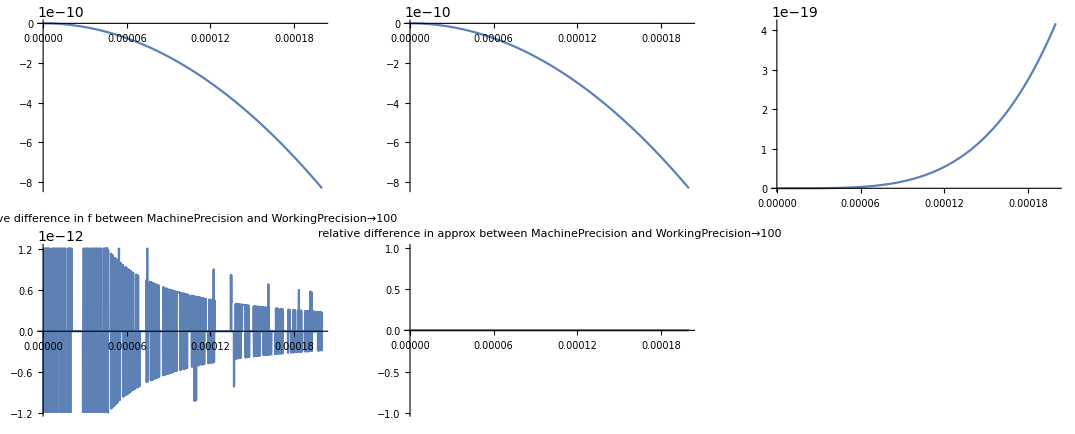

```mathematica
singAnal[Sin[#/2]/#&, criticalPoint->0, thresholdForApproximation->1 10^-4,degreeOfApproximation-> 3,direction->"Right"]
```

Function: f[x] = Sin[x]/x

{x>0}

Limit: (lim_(x→))_0 f[x] = 1

Taylor approximation: f[x] = 1-x^2/6+O[x]^4

Maximal difference to approximation inside the threshold: 8.33333×10^-19

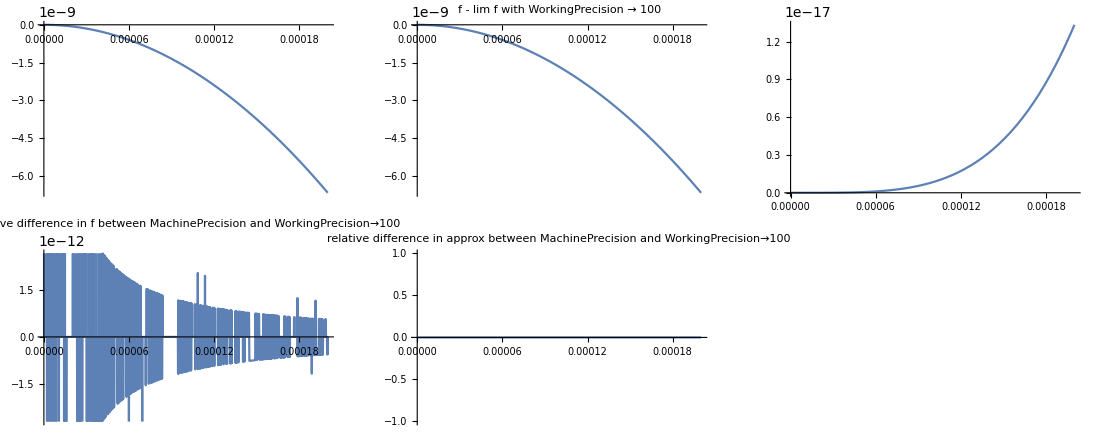

```mathematica
singAnal[Sin[#]/#&, criticalPoint->0, thresholdForApproximation->1 10^-4,degreeOfApproximation-> 3,direction->"Right"]
```

Function: f[x] = (1-Cos[x])/x^2

{x>0}

Limit: (lim_(x→))_0 f[x] = 1/2

Taylor approximation: f[x] = 1/2-x^2/24+x^4/720+O[x]^6

Maximal difference to approximation inside the threshold: 2.48016×10^-17

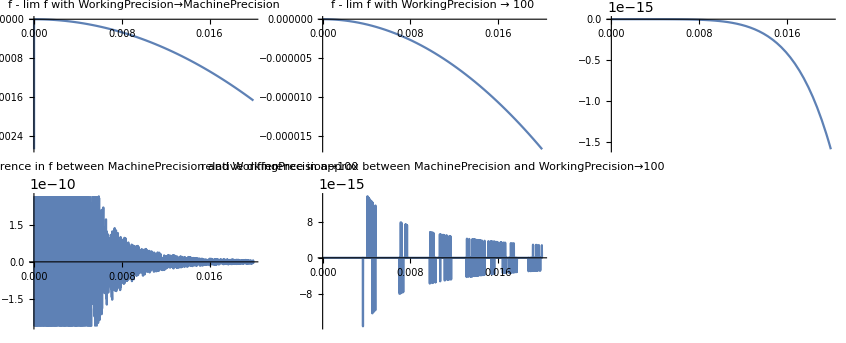

```mathematica
singAnal[(1-Cos[#])/#^2&, criticalPoint->0, thresholdForApproximation->1 10^-2,degreeOfApproximation-> 5,direction->"Right"]
```

Function: f[x] = (-1+Cos[x])/x^2

{x>0}

Limit: (lim_(x→))_0 f[x] = -1/2

Taylor approximation: f[x] = -1/2+x^2/24-x^4/720+O[x]^6

Maximal difference to approximation inside the threshold: 2.48016×10^-17

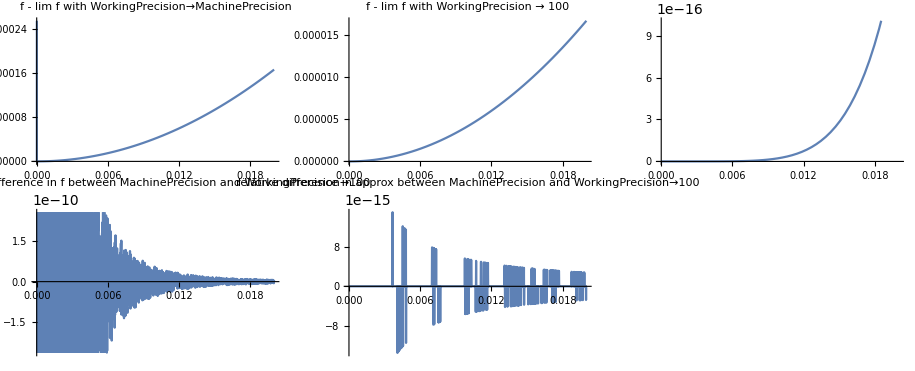

```mathematica
singAnal[(Cos[#] - 1)/#^2&, criticalPoint->0, thresholdForApproximation->1 10^-2,degreeOfApproximation-> 5,direction->"Right"]
```

Function: f[x] = (x-Sin[x])/x^3

{x>0}

Limit: (lim_(x→))_0 f[x] = 1/6

Taylor approximation: f[x] = 1/6-x^2/120+x^4/5040+O[x]^6

Maximal difference to approximation inside the threshold: 2.75573×10^-18

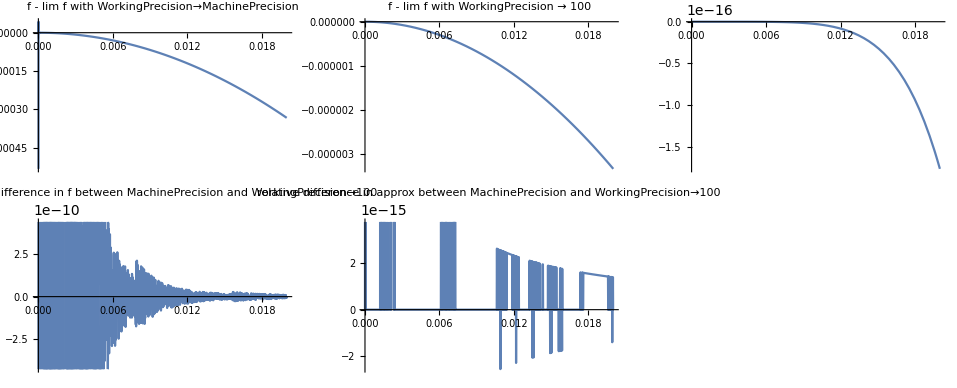

```mathematica
singAnal[(#-Sin[#])/#^3&, criticalPoint->0, thresholdForApproximation->1 10^-2,degreeOfApproximation-> 5,direction->"Right"]
```

Function: f[x] = (2-2 Cos[x]-x Sin[x])/x^4

{x>0}

Limit: (lim_(x→))_0 f[x] = 1/12

Taylor approximation: f[x] = 1/12-x^2/180+x^4/6720-x^6/453600+O[x]^8

Maximal difference to approximation inside the threshold: 2.08754×10^-16

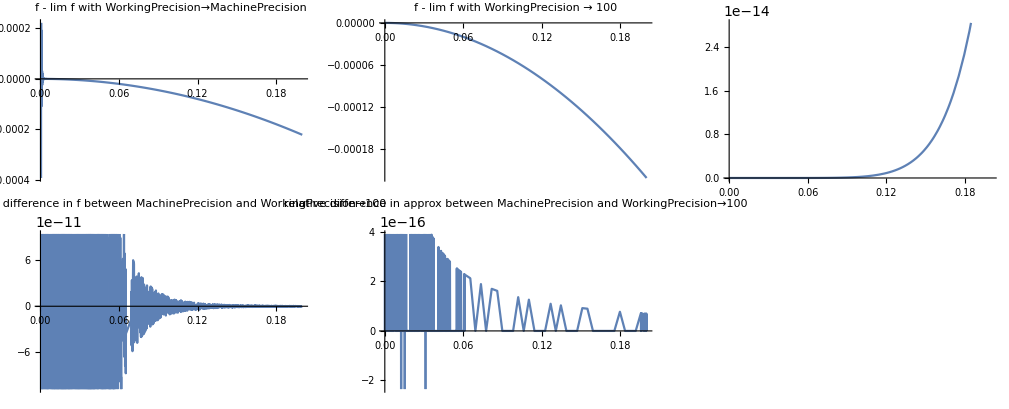

```mathematica
singAnal[(2 - 2 Cos[#]- # Sin[#])/#^4&, criticalPoint->0, thresholdForApproximation-> 10^-1,degreeOfApproximation-> 7,direction->"Right"]
```

Function: f[x] = (x (2+Cos[x])-3 Sin[x])/x^5

{x>0}

Limit: (lim_(x→))_0 f[x] = 1/60

Taylor approximation: f[x] = 1/60-x^2/1260+x^4/60480-x^6/4989600+O[x]^8

Maximal difference to approximation inside the threshold: 1.60581×10^-17

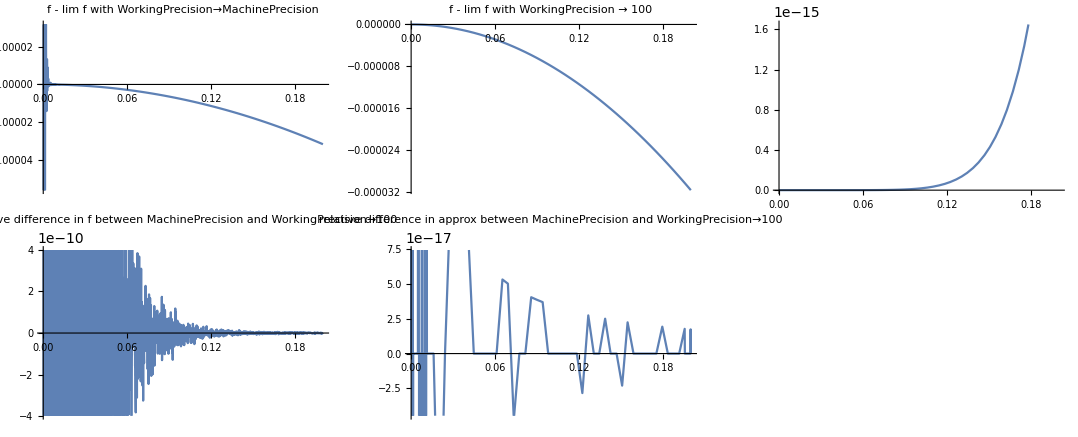

```mathematica
singAnal[(# (2 + Cos[#]) - 3 Sin[#])/#^5&, criticalPoint->0, thresholdForApproximation-> 10^-1,degreeOfApproximation-> 7,direction->"Right"]
```

Function: f[x] = (2-x Cot[x/2])/(2 x^2)

{x>0}

Limit: (lim_(x→))_0 f[x] = 1/12

Taylor approximation: f[x] = 1/12+x^2/720+x^4/30240+O[x]^6

Maximal difference to approximation inside the threshold: 8.26722×10^-19

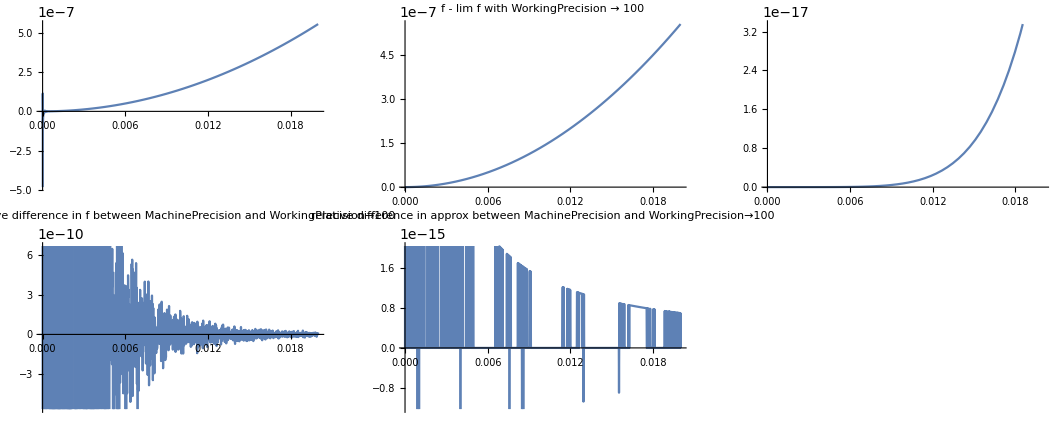

```mathematica
singAnal[(2 - #/Tan[#/2])/(2#^2)&, criticalPoint->0, thresholdForApproximation-> 10^-2,degreeOfApproximation-> 5,direction->"Right"]
```

Function: f[x] = (2 ArcCos[x])/(√(1-x^2))

{x<1}

Limit: (lim_(x→))_1 f[x] = 2

Taylor approximation: f[x] = 2-(2 (x-1))/3+4/15 (x-1)^2-4/35 (x-1)^3+16/315 (x-1)^4-16/693 (x-1)^5+O[x-1]^6

Maximal difference to approximation inside the threshold: 1.6689×10^-16

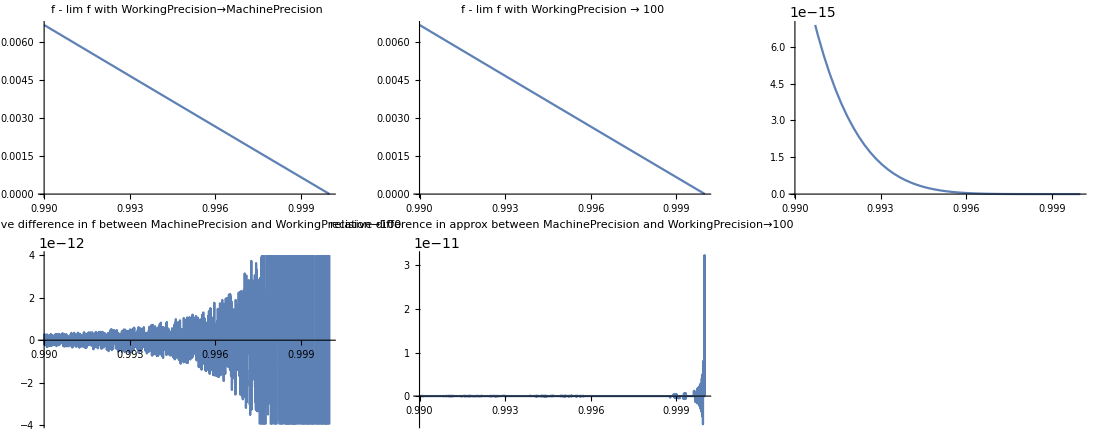

```mathematica
singAnal[2 ArcCos[#]/Sqrt[1-#^2]&, criticalPoint->1, thresholdForApproximation-> 5 10^-3,degreeOfApproximation-> 5,direction->"Left"]
```

Function: f[x] = (Csc[x/2]^2 (-4+x^2+4 Cos[x]+x Sin[x]))/(4 x^4)

{x>0}

Limit: (lim_(x→))_0 f[x] = 1/360

Taylor approximation: f[x] = 1/360+x^2/7560+x^4/201600+x^6/5987520+(691 x^8)/130767436800+O[x]^9

Maximal difference to approximation inside the threshold: 1.64639×10^-17

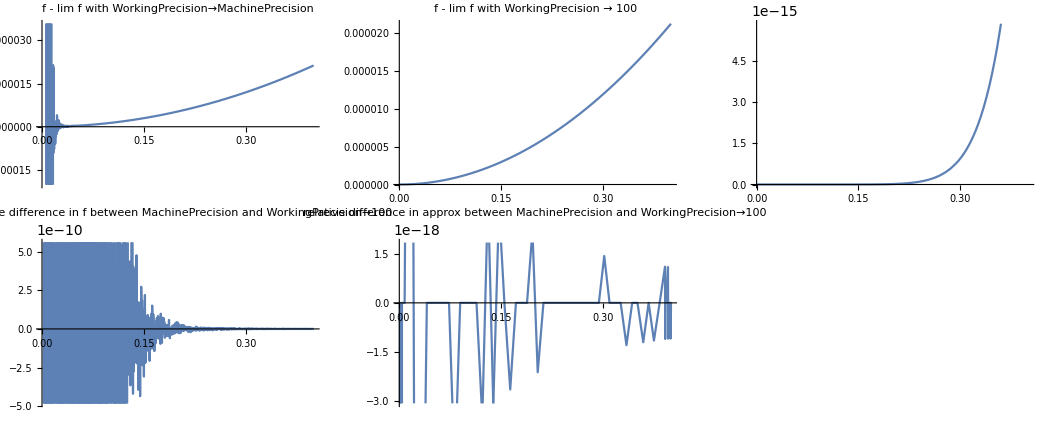

```mathematica
singAnal[(# Sin[#] + 4 Cos[#] + #^2 - 4)/(4Sin[#/2]^2 #^4)&, criticalPoint->0, thresholdForApproximation-> 2 10^-1,degreeOfApproximation-> 8,direction->"Right"]
```

```mathematica
N[691/130767436800,16]//FortranForm
```

5.284190138687493e-9

Function: f[x] = (64-12 x Cot[x/2]+(4 x^2 (3+x Cot[x/2]))/(-1+Cos[x]))/(8 x^6)

{x>0}

Limit: (lim_(x→))_0 f[x] = 1/3780

Taylor approximation: f[x] = 1/3780+x^2/50400+x^4/997920+(691 x^6)/16345929600+O[x]^7

Maximal difference to approximation inside the threshold: 1.05845×10^-12

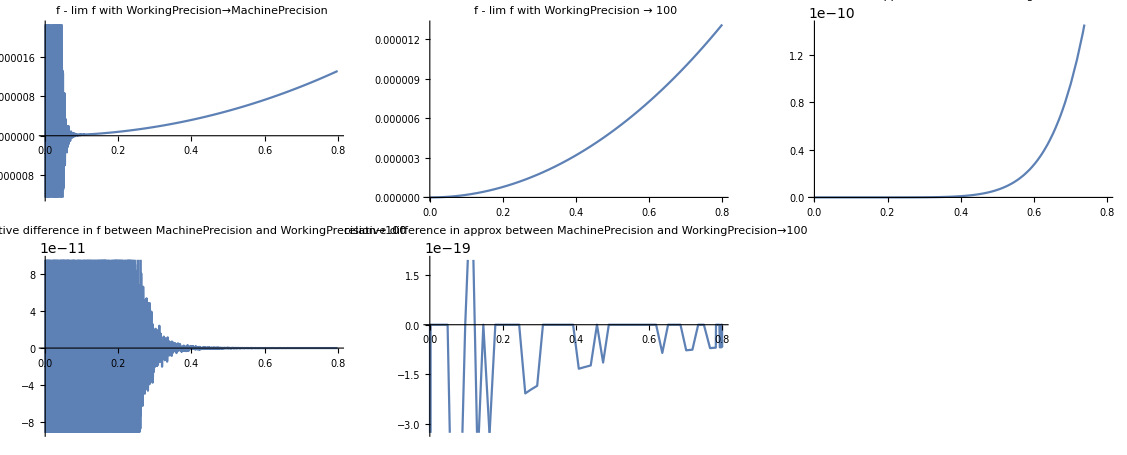

```mathematica
singAnal[(64-12 # Cot[#/2]+(4 #^2 (3+# Cot[#/2]))/(-1+Cos[#]))/(8 #^6)&, criticalPoint->0, thresholdForApproximation-> 4 10^-1,degreeOfApproximation-> 6,direction->"Right"]
```